-Graphics3D-

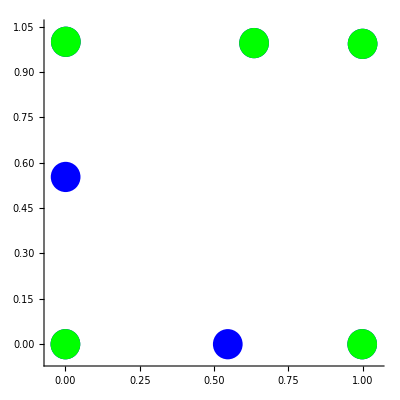

```mathematica
sr=0.05;
points=
{

};
aufpunkt = 
erster_pfeil=
zweiter_pfeil=
neuer_aufpunkt=
erster_bounding=
zweiter_bounding=
texcoords=
{

};
minmalpunkt=
deleted_texcoords=
{

};
sorted_points=
{
};
Graphics3D[
{
Blue,
Map[Sphere[#1,sr]&,points],
Blue,
Arrow[aufpunkt,aufpunkt + erster_pfeil],
Arrow[aufpunkt,aufpunkt + zweiter_pfeil],
Green,
Arrow[neuer_aufpunkt,neuer_aufpunkt + erster_pfeil],
Arrow[neuer_aufpunkt,neuer_aufpunkt + zweiter_pfeil],
Red,
Arrow[neuer_aufpunkt,neuer_aufpunkt + erster_bounding],
Arrow[neuer_aufpunkt,neuer_aufpunkt + zweiter_bounding],
Line[sorted_points]
}
]

Graphics[
{
Blue,
Map[Disk[#1,sr]&,texcoords],
Green,
Disk[minimalpunkt,sr],
Red,
Map[Disk[#1,sr]&,deleted_texcoords],
},
Axes->True
]
```